```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/silvestre_parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
On[Assert]
```

```mathematica
ClearAll[J,P,Isospin,γMax,Λ,m1,m2,m3,projector,project,size,firstNonZero,ham,sM,t1,t2]
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=1;(* Isospin *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
m1=bq;(* mass of quark 1 *)
m2=bq;(* mass of quark 2 *)
m3=uq;(* mass of quark 3 *)
excited=0;(* Choose excited state, 0 for ground state *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
project=If[m1==m2,True,False];
(* Obtain projector matrix *)
projector=Projector[J,P,Λ,γMax,Isospin];
(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,γMax,m1,m2,m3,1]];
Print["Time taken to compute t1: ",t1time]
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,γMax,m1,m2,m3,2]];
Print["Time taken to compute t2: ",t2time]
(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];
(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
firstNonZero=If[project==True,size-Total[Diagonal[projector]]+excited+1,1+excited];
ham[ω_]:=Hb[J,P,Isospin,Λ,γMax,ω,m1,m2,m3,project];
sM=stateMatrix[J,P,Λ,γMax];
```

Time taken to compute t1: 0.055049

Time taken to compute t2: 0.049949

Time taken to find minimum: 8.01195s

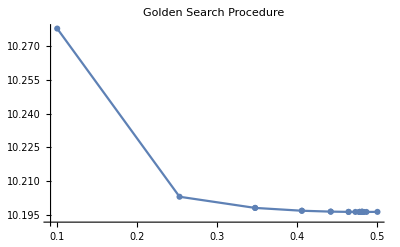

{ω_min,E_min}: {0.480720.00024,10.1961}

Expectation Values of √(<SuperscriptBox[SubscriptBox[ρ, i], 2]>) for pairs {12, 23, 31} in (fm): {0.295794,0.656745,0.656745}

Expectation Values as ratios: {0.450393,1.,1.}

Expectation Values of <λ_i^2> {λ_3, λ_1, λ_2} in (fm^2): {0.409441,0.0839144,0.0839144}

Expectation Values as ratios: {1.,0.204949,0.204949}

```mathematica
ClearAll[minTime,a,b,wMin,eigvalMin,evec,rhoSqrd12,rhoSqrd23,rhoSqrd31,rhos,expValsRho,lamSqrd12,lamSqrd23,lamSqrd31,lams,expValsLam]
(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,firstNonZero,0.1,0.5,0.0005]];
wMin=(a+b)/2;
Print["Time taken to find minimum: ",minTime,"s"]
ListPlot[Sort[data],PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotLabel->"Golden Search Procedure"]
eigvalMin=Eigenvalues[ham[wMin]][[-firstNonZero]];
Print["{ω_min,E_min}: ",{Around[wMin,a-wMin],eigvalMin}]
(* Obtain eigenvector of total hamiltonian *)
evec=Eigenvectors[ham[wMin]][[-firstNonZero]];
(* Find expectation values of <ρ^2> *)
rhoSqrd12=1/α[m1,m2,wMin]^2 polynomialOperatorRho[sM,2];
rhoSqrd23=1/α1[m1,m2,m3,wMin]^2 Transpose[t1].polynomialOperatorRho[sM,2].t1;
rhoSqrd31=1/α2[m1,m2,m3,wMin]^2 Transpose[t2].polynomialOperatorRho[sM,2].t2;
rhos={rhoSqrd12,rhoSqrd23,rhoSqrd31};
expValsRho=Table[evec.rhos[[i]].evec,{i,1,3}];
Print["Expectation Values of √(<SuperscriptBox[SubscriptBox[ρ, i], 2]>) for pairs {12, 23, 31} in (fm): ",√expValsRho/5.068]
Print["Expectation Values as ratios: ",√expValsRho/√Max[expValsRho]]
(* Find expectation values of <λ^2> *)
lamSqrd12=1/β[m1,m2,m3,wMin]^2 polynomialOperatorLambda[sM,2];
lamSqrd23=1/β1[m1,m2,m3,wMin]^2 Transpose[t1].polynomialOperatorLambda[sM,2].t1;
lamSqrd31=1/β2[m1,m2,m3,wMin]^2 Transpose[t2].polynomialOperatorLambda[sM,2].t2;
lams={lamSqrd12,lamSqrd23,lamSqrd31};
expValsLam=Table[evec.lams[[i]].evec,{i,1,3}];
Print["Expectation Values of <λ_i^2> {λ_3, λ_1, λ_2} in (fm^2): ",expValsLam/5.068^2]
Print["Expectation Values as ratios: ",expValsLam/expValsLam[[1]]]
```

```mathematica
(* Mean mass-square radius using exact method *)
expVals=expValsLam/5.068^2;
λ3Squared=expVals[[1]];
λ1Squared=expVals[[2]];
λ2Squared=expVals[[3]];
M=m1+m2+m3;
term1=(m1(m2+m3)^2)/M^3 λ1Squared;
term2=(m2(m1+m3)^2)/M^3 λ2Squared;
term3=(m3(m1+m2)^2)/M^3 λ3Squared;
RmSquared=term1+term2+term3
```

0.0947281

```mathematica
(* Excited states and how their size grows *)
baryon="ubb";
lengths={
{0.657,0.296,0.657},
{0.738,0.580,0.738},
{0.851,0.776,0.851},
{0.997,0.504,0.997},
{1.208,0.314,1.208},
{1.014,0.906,1.014}
};
Export["plots/Silvestre/triangles/lengths/ubb.mx",lengths]

excitedTriangle[i_]:=Module[{},
{q1,q2,q3}=StringTake[baryon,{{1},{2},{3}}];
{p12,p23,p31}=lengths[[i]];
t=SSSTriangle[p23,p12,p31];
{cx,cy}=RegionCentroid[t];

AppendTo[t[[1]],{0.000001,0.0000001}];

SetOptions[ListLinePlot,PlotStyle->{Gray,Dashed},BaseStyle->{FontFamily->"Times",FontSize->12},AspectRatio->Automatic];

ListLinePlot[t[[1]]->{q1,q3,q2,None},
Axes->None,
PlotRange->{{-0.3,1.5},{-0.1,1.0}},
LabelingFunction->Automatic,
PlotMarkers->{●, 8},
PlotLegends->{Placed["n="<>ToString[i-1],{0,0.9}]},
LabelStyle->{FontFamily->"Times"}]
]
color=Gray//Lighter;
t=Grid[Table[excitedTriangle[3i+j+1],{i,0,1},{j,0,2}],ItemSize->All,Dividers->{{2->{color},3->{color}},{2->{color}}}]
Export["plots/Silvestre/triangles/ubbExcited.pdf",t]
```

plots/Silvestre/triangles/lengths/ubb.mx

-Graphics-

plots/Silvestre/triangles/ubbExcited.pdf

```mathematica
(* Random, unexcited states *)
baryons={
{"udc",{0.770,0.707,0.707}},
{"uuc",{0.924,0.751,0.751}},
{"udb",{0.764,0.675,0.675}},
{"uub",{0.930,0.739,0.739}},
{"ubb",{0.657,0.296,0.657}},
{"ccb",{0.426,0.368,0.368}}
};
fontColour=Gray//Darker;
names={
Style["Λ_c",Bold,fontColour],
Style["Σ_c",Bold,fontColour],
Style["Λ_b",Bold,fontColour],
Style["Σ_b",Bold,fontColour],
Style["Ξ_bb",Bold,fontColour],
Style["Ω_ccb",Bold,fontColour]
};
triangle[i_]:=Module[{quarks,t,cx,cy},
quarks=baryons[[i,1]];
{p12,p23,p31}=baryons[[i,2]];
{q1,q2,q3}=StringTake[quarks,{{1},{2},{3}}];
t=SSSTriangle[p23/0.924,p12/0.924,p31/0.924];
{cx,cy}=RegionCentroid[t];

AppendTo[t[[1]],{0.000001,0.0000001}];

SetOptions[ListLinePlot,PlotStyle->{Gray,Dashed},BaseStyle->{FontFamily->"Times",FontSize->12},AspectRatio->Automatic];

ListLinePlot[t[[1]]->{q1,q3,q2,None},Axes->None,PlotRange->{{-0.2,1},{-0.05,0.9}},LabelingFunction->Automatic,PlotMarkers->{●, 8},PlotLegends->Placed[names[[i]],{0.1,0.9}]]
]
color=Gray//Lighter;
t=Grid[Table[triangle[3i+j+1],{i,0,1},{j,0,2}],ItemSize->All,Dividers->{{2->{color},3->{color}},{2->{color}}}]
Export["plots/Silvestre/triangles/randomUnexcited.pdf",t]
```

-Graphics-

plots/Silvestre/triangles/randomUnexcited.pdf